```mathematica
Lab 2
Variant 5
```

```mathematica
F[x_, u_]:= (u^2(2-Log[x]))/x^2;
Subscript[u, 0] = 1;
x0 = 1;
b= 2;
n=100;
X={};
h=(b-x0)/n;
For[k=0, k<n, k++,
AppendTo[X,x0+k*h //N]; (* Сформировали сетку Х *)
]
Print["X=", X];
Y={};
For[k=0, k<n, k++,
AppendTo[Y,0]; 
]
Y⟦1⟧=Subscript[u, 0];
Print["Y=", Y];
For[k=1, k<n, k++,
K1=h*F[ X⟦k⟧, Y⟦k⟧ ]//N;
K2=h*F[ X⟦k⟧+h/2, Y⟦k⟧ +K1/2]//N;
K3=h*F[ X⟦k⟧+h/2, Y⟦k⟧+K2/2 ]//N;
K4=h*F[ X⟦k⟧+h, Y⟦k⟧+K3 ]//N;
Y⟦k+1⟧=Y⟦k⟧+1/6*(K1+2*K2+2*K3+K4)//N; 
]
Print["Y=",Y];
Res={};
For[k=1, k≤  n, k++,
AppendTo[Res, {X⟦k⟧, Y⟦k⟧}];
]
Print["Res=",Res];
```

X={1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.13,1.14,1.15,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.38,1.39,1.4,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.63,1.64,1.65,1.66,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.88,1.89,1.9,1.91,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99}

Y={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Y={1,1.02015,1.04061,1.06137,1.08245,1.10386,1.12559,1.14765,1.17005,1.19279,1.21589,1.23934,1.26315,1.28734,1.3119,1.33684,1.36217,1.38791,1.41404,1.4406,1.46757,1.49497,1.52281,1.5511,1.57984,1.60905,1.63873,1.66889,1.69955,1.73071,1.76239,1.79459,1.82732,1.86061,1.89445,1.92886,1.96386,1.99945,2.03565,2.07247,2.10993,2.14805,2.18683,2.22629,2.26644,2.30731,2.34892,2.39126,2.43438,2.47828,2.52298,2.56851,2.61488,2.66211,2.71023,2.75926,2.80922,2.86014,2.91204,2.96495,3.01889,3.07389,3.12999,3.1872,3.24557,3.30512,3.36589,3.42792,3.49123,3.55586,3.62186,3.68927,3.75812,3.82846,3.90034,3.9738,4.0489,4.12568,4.20419,4.28451,4.36667,4.45075,4.5368,4.6249,4.71511,4.80751,4.90217,4.99918,5.09861,5.20055,5.3051,5.41235,5.5224,5.63537,5.75135,5.87048,5.99287,6.11865,6.24797,6.38096}

Res={{1.,1},{1.01,1.02015},{1.02,1.04061},{1.03,1.06137},{1.04,1.08245},{1.05,1.10386},{1.06,1.12559},{1.07,1.14765},{1.08,1.17005},{1.09,1.19279},{1.1,1.21589},{1.11,1.23934},{1.12,1.26315},{1.13,1.28734},{1.14,1.3119},{1.15,1.33684},{1.16,1.36217},{1.17,1.38791},{1.18,1.41404},{1.19,1.4406},{1.2,1.46757},{1.21,1.49497},{1.22,1.52281},{1.23,1.5511},{1.24,1.57984},{1.25,1.60905},{1.26,1.63873},{1.27,1.66889},{1.28,1.69955},{1.29,1.73071},{1.3,1.76239},{1.31,1.79459},{1.32,1.82732},{1.33,1.86061},{1.34,1.89445},{1.35,1.92886},{1.36,1.96386},{1.37,1.99945},{1.38,2.03565},{1.39,2.07247},{1.4,2.10993},{1.41,2.14805},{1.42,2.18683},{1.43,2.22629},{1.44,2.26644},{1.45,2.30731},{1.46,2.34892},{1.47,2.39126},{1.48,2.43438},{1.49,2.47828},{1.5,2.52298},{1.51,2.56851},{1.52,2.61488},{1.53,2.66211},{1.54,2.71023},{1.55,2.75926},{1.56,2.80922},{1.57,2.86014},{1.58,2.91204},{1.59,2.96495},{1.6,3.01889},{1.61,3.07389},{1.62,3.12999},{1.63,3.1872},{1.64,3.24557},{1.65,3.30512},{1.66,3.36589},{1.67,3.42792},{1.68,3.49123},{1.69,3.55586},{1.7,3.62186},{1.71,3.68927},{1.72,3.75812},{1.73,3.82846},{1.74,3.90034},{1.75,3.9738},{1.76,4.0489},{1.77,4.12568},{1.78,4.20419},{1.79,4.28451},{1.8,4.36667},{1.81,4.45075},{1.82,4.5368},{1.83,4.6249},{1.84,4.71511},{1.85,4.80751},{1.86,4.90217},{1.87,4.99918},{1.88,5.09861},{1.89,5.20055},{1.9,5.3051},{1.91,5.41235},{1.92,5.5224},{1.93,5.63537},{1.94,5.75135},{1.95,5.87048},{1.96,5.99287},{1.97,6.11865},{1.98,6.24797},{1.99,6.38096}}

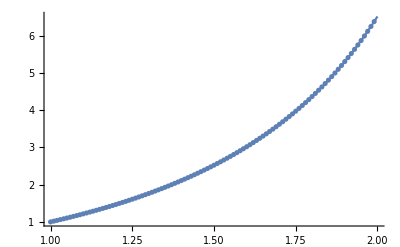

```mathematica
u[x_]:= x/(1-Log[x]);
G1 = Plot[u[x], {x,x0, b}];
G2 = ListPlot[Res];
Show[G1, G2]
```